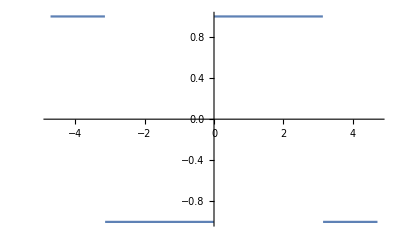

```mathematica
Plot[SquareWave[{-1,1}, x/(2*Pi)], {x, -3*Pi/2, 3*Pi/2}]
```

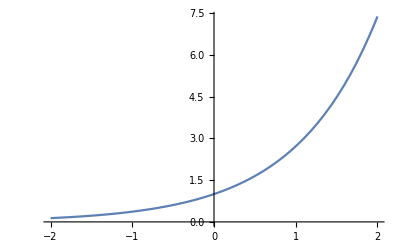

```mathematica
p = Plot[Exp[x],{x, -2,2}]
```

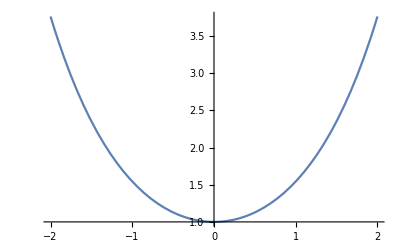

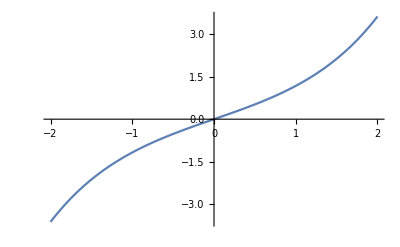

-Graphics-

```mathematica
f[x_]:= Exp[x];
geven[x_] := (f[x] + f[-x])/2;
godd[x_] := (f[x] - f[-x])/2;
Plot[geven[x],{x, -2, 2}]
Plot[godd[x],{x, -2, 2}]
Plot[geven[x] + godd[x],{x, -2, 2}]
```